# MU Mathematica Workshop

## Basic Navigation

Use SHIFT + ENTER to evaluate a cell

```mathematica
4+1
```

Use ENTER to add a new line

```mathematica
a=4+1
b=a+2
b
```

Supress displaying output using a ; at the end

```mathematica
longlist = Table[n^2,{n,0,1000}];
```

use F1 or “Help” → “Find Selected Function” to get documentation for functions like Series and BesselJ

```mathematica
Series[BesselJ[0,x],{x,0,10}]
```

## Variables

Variables start with letters or $

Stick with lower case as uppercase is saved for in-built functions so camelCase is popular for naming

Use “=” (Set) for variables

Use Clear[variable]

```mathematica
c=5
Clear[c]
c
```

Use Clear[“Global`*”]

```mathematica
{a,b,c} = {1,2,3}
Clear["Global`*"]
{a,b,c}
```

{1,2,3}

{a,b,c}

## Basic Arithmetic

Standard + - * / ^ work as expected

Use () or {} as delimiters (do not use [])

Use CTRL + ^ or CTRL + / for graphic interpretation of exponent/division

```mathematica
fraction = num/denom;
```

Space between defaults to multiplication

```mathematica
a=5;
b=3;
a b
```

15

Substitition can be done many ways, but most common is using /. and the assignment -> (hyphen + right angle bracket)

```mathematica
expression = e^2+f^2+m x
expression /. e->4
expression /. {e->4, f->3}
```

e^2+f^2+m x

25+m x

## Functions

Underscore to identify variables in expression
Use := (Set Delay) for functions so it isn’t evaluated on output away

```mathematica
f[x_]:=x^2
g[x_,upperbound_] := Total[Table[x^n/(n^2+1),{n,0,upperbound}]]
```

Built-in functions use the same Function[parameters] notation

```mathematica
Sin[Pi/2]
Table[i^2,{i,1,10}]
```

1

{1,4,9,16,25,36,49,64,81,100}

## Lists / Vectors

Curly brackets denote a vector

```mathematica
v1 = {1,2,3};
v2 = {4,5,6};
```

```mathematica
Cross[v1,v2]
Dot[v1,v2]
VectorAngle[v1,v2]
```

{-3,6,-3}

32

ArcCos[(16 √(2/11))/7]

Multivariable functions are also described by vectors

```mathematica
field = {Sin[x],Cos[y],z};
Grad[field,{x,y,z}]
```

{{Cos[x],0,0},{0,-Sin[y],0},{0,0,1}}

## Arrays / Matrices

Matrices are considered vectors of vectors

```mathematica
m1 = {v1,{0,22,16}, {0,-9,-2}}
```

{{1,2,3},{0,22,16},{0,-9,-2}}

Many matrix operations are built into Mathematica:

```mathematica
Det[m1]
Inverse[m1]
{m1Eigenvalues, m1Eigenvectors} =Eigensystem[m1]
```

100

{{1,-23/100,-17/50},{0,-1/50,-4/25},{0,9/100,11/50}}

{{10,10,1},{{1,-36,27},{0,0,0},{1,0,0}}}

Use MatrixForm[] to visualise a matrix easier

```mathematica
MatrixForm[m1]
```

(1 | 2 | 3
0 | 22 | 16
0 | -9 | -2)

## Calculus and ODEs

Differentiation is done via D[f,x] or D[f,{x,n}]

```mathematica
D[x^11,x]
D[x^11,{x,10}]
D[x y+Sin[x^2y],x,y]
```

11 x^10

39916800 x

1+2 x Cos[x^2 y]-2 x^3 y Sin[x^2 y]

Similarly, we can integrate via Integrate[f,x] or Integrate[f,{x,a,b}]

```mathematica
Integrate[Sin[Pi x],x]
Integrate[Sin[Pi x],{x,2,3}]
```

-Cos[π x]/π

2/π

And again, with solving differential equations, we have DSolve[ODE,y[x],x]

Use == as we are solving for being equal to zero

```mathematica
ODEField = y''[x]+y[x];
DSolve[ODEField==0,y[x],x]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

Initial conditions are given as another equation, so we use curly brackets to solve multiple equations

```mathematica
DSolve[
{ODEField==0, y[0]==2,y[1]==1}, (* two equations specified here *)
y[x],x]
```

{{y[x]→2 Cos[x]-2 Cot[1] Sin[x]+Csc[1] Sin[x]}}

## Numerical Solutions and Simplification

If you need to simplify/transform your expression somehow, Mathematica can probably do it if you search the documentation. See also Expand, Factor, FullSimplify, Solve, Rationalize, NDSolve, NSolve

```mathematica
exampleIntegral = Integrate[x^3+x-1/x,{x,1,2}];
N[exampleIntegral] 

(* Useful for integrals without closed forms *)
NIntegrate[x^3+x-1/x,{x,1,2}]
```

4.55685

4.55685

```mathematica
exampleFraction = 1/(4 (-1+x))-1/(4 (1+x))-1/(2 (1+x^2));
Simplify[exampleFraction]
```

1/(-1+x^4)

## Plotting

Plotting essentially has the same syntax across all plotting types:

Plots can also be saved as variables and combined/tweaked using Show[plot,options]

See documentation of Plot for all parameters you can play with

x^2+y

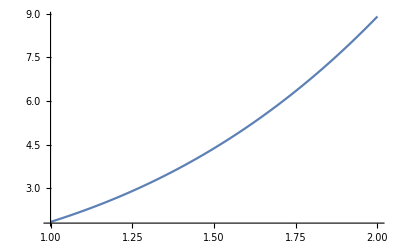

```mathematica
function1 = x^3+Sin[x];
function2 =x^2;
function3=x^2+y 

Plot[function1,{x,1,2}]
```

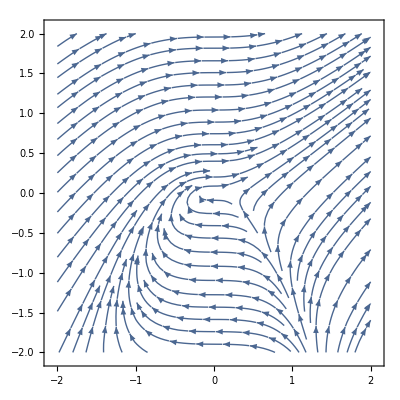

```mathematica
StreamPlot[{function3,function2},{x,-2,2},{y,-2,2}]
```

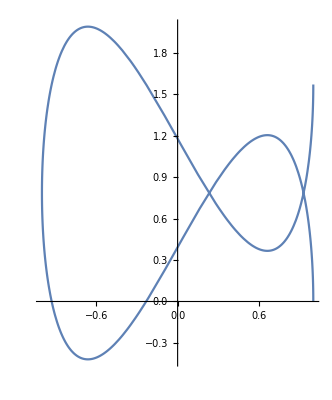

```mathematica
vectorCoord = {Cos[t],Sin[2t]+t/4};
ParametricPlot[ vectorCoord,{t,0,2 Pi}]
```